```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\VS_workspace\CPlusPlus\SOHR\projects\catalytic_cycle\theory\wall_S_chattering_problem

## A⇌_k2^k1 B⟶^k3 C problem

### Solve differential equation like d[A]/dt=-k1[A]+k2[B] d[B]/dt=k1[A]-k2[B]-k3[B] d[C]/dt=k3[B]

```mathematica
(*left hand side of equation in terms of k1, k2, k3 and t, Here we calculate the concentration of C*)
Clear[ExactSolnC];ExactSolnC[k1_,k2_,t_,k3_]:=
Module[{soln,output,x1,x2,x3},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] - (k2 +k3)* x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
output=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[output];]
```

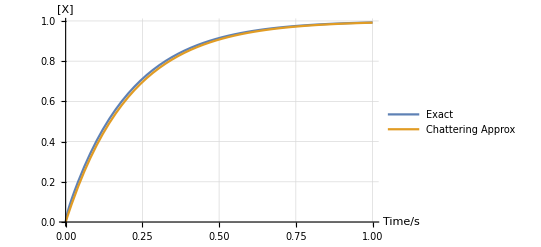

```mathematica
Value1={k1->10^14,k2->10^14,k3->10^13};Plot[{ExactSolnC[k1,k2,t,k3]/.Value1//Evaluate,1-ⅇ^(-(k3*k1/(k3+k1+k2))*t)/.Value1},{t,0, 10^-12},PlotLegends->{"Exact","Chattering Approx"},GridLines->Automatic,AxesLabel->{"Time/s","[X]"}]
```

```mathematica
Clear[PLOTERROR];PLOTERROR[kbasein_,endTime_,λin_]:=Module[
{k1,k2,k3,λ,t,Value1,kbase},
Value1={k1->λ*kbase,k2->λ*kbase,k3->kbase}/.{kbase->kbasein,λ->λin};Plot[(ExactSolnC[k1,k2,t,k3]-(1-ⅇ^(-(k3*k1/(k3+k1+k2))*t)))/ExactSolnC[k1,k2,t,k3]/.Value1//Evaluate,{t,0, endTime},PlotLegends->{"Relative Error"},GridLines->Automatic,AxesLabel->{"Time/s","[X]"},PlotLabel->"λ="<>ToString[N[λin]]]];
```

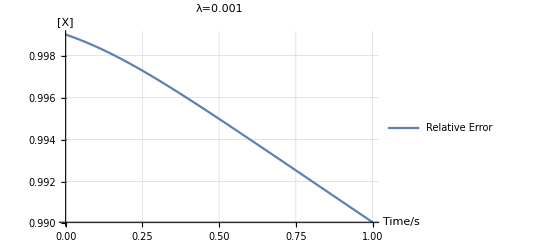

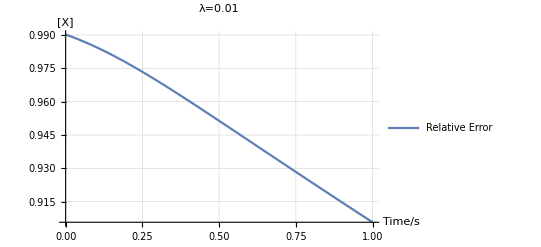

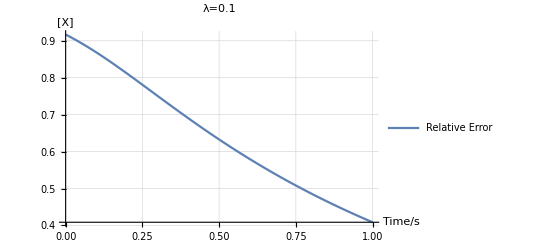

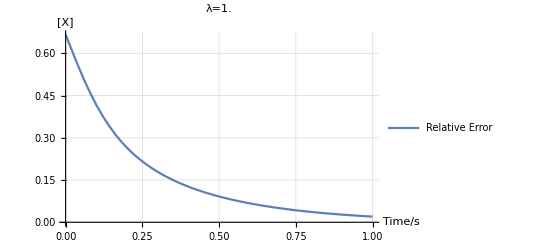

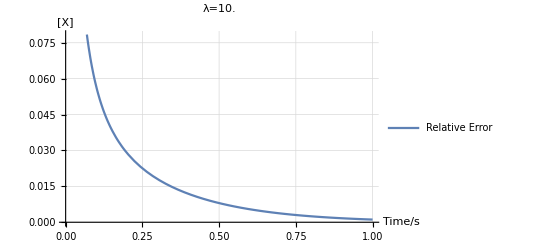

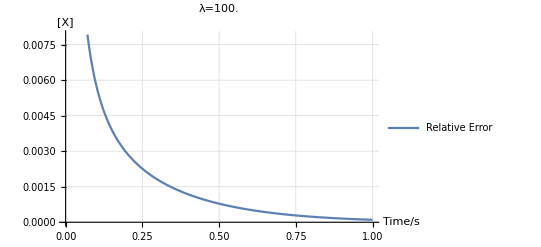

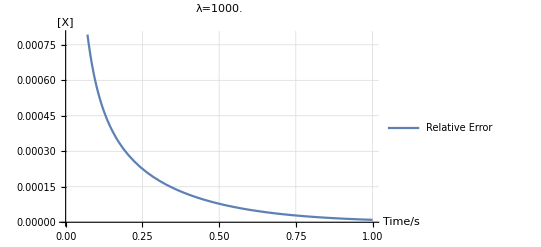

```mathematica
PLOTERROR[10^13,10^-12,10^-3]
PLOTERROR[10^13,10^-12,10^-2]
PLOTERROR[10^13,10^-12,10^-1]
PLOTERROR[10^13,10^-12,10^-0]
PLOTERROR[10^13,10^-12,10^1]
PLOTERROR[10^13,10^-12,10^2]
PLOTERROR[10^13,10^-12,10^3]
```